```mathematica
Map[ShowGraph2,Select[Keys[allGraphs5],EdgeCount[allGraphs5[#,"graph"]]==9&]]
```

{-Graphics-295230,-Graphics-295210,-Graphics-295150,-Graphics-294970,-Graphics-294430,-Graphics-292810,-Graphics-287950,-Graphics-273370,-Graphics-229630,-Graphics-98410}

```mathematica
Map[ShowGraph2, Select[Keys[allGraphs5],allGraphs5[#,"atleast"]==0&]]
```

{-Graphics-295200,-Graphics-295230,-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295210,-Graphics-295330,-Graphics-295140,-Graphics-295150,-Graphics-295120,-Graphics-295420,-Graphics-295510,-Graphics-295600,-Graphics-294930,-Graphics-294960,-Graphics-294970,-Graphics-294940,-Graphics-295740,-Graphics-296020,-Graphics-296050,-Graphics-296080,-Graphics-296330,-Graphics-295770,-Graphics-294390,-Graphics-294420,-Graphics-294430,-Graphics-294460,-Graphics-294400,-Graphics-294330,-Graphics-294340,-Graphics-294310,-Graphics-294600,-Graphics-294690,-Graphics-294160,-Graphics-297670,-Graphics-297970,-Graphics-292810,-Graphics-292780,-Graphics-292720,-Graphics-292690,-Graphics-292960,-Graphics-293050,-Graphics-292540,-Graphics-292570,-Graphics-292000,-Graphics-291970,-Graphics-292230,-Graphics-291730,-Graphics-291760,-Graphics-302530,-Graphics-303340,-Graphics-287910,-Graphics-287940,-Graphics-287950,-Graphics-287920,-Graphics-287640,-Graphics-287670,-Graphics-287680,-Graphics-287650,-Graphics-288450,-Graphics-288730,-Graphics-288760,-Graphics-288480,-Graphics-317080,-Graphics-317110,-Graphics-317140,-Graphics-317380,-Graphics-316840,-Graphics-319540,-Graphics-319840,-Graphics-314650,-Graphics-314680,-Graphics-314920,-Graphics-314410,-Graphics-314440,-Graphics-273330,-Graphics-273360,-Graphics-273370,-Graphics-273400,-Graphics-273340,-Graphics-273270,-Graphics-273280,-Graphics-273250,-Graphics-273550,-Graphics-273640,-Graphics-273090,-Graphics-273100,-Graphics-272550,-Graphics-272560,-Graphics-272460,-Graphics-272470,-Graphics-272730,-Graphics-272820,-Graphics-266080,-Graphics-266050,-Graphics-265810,-Graphics-360570,-Graphics-360840,-Graphics-360850,-Graphics-360860,-Graphics-361120,-Graphics-360580,-Graphics-361380,-Graphics-361660,-Graphics-361940,-Graphics-360030,-Graphics-360040,-Graphics-360300,-Graphics-368170,-Graphics-368980,-Graphics-353250,-Graphics-353520,-Graphics-353530,-Graphics-353260,-Graphics-354060,-Graphics-354340,-Graphics-382810,-Graphics-383080,-Graphics-338880,-Graphics-338890,-Graphics-339160,-Graphics-338070,-Graphics-338080,-Graphics-338340,-Graphics-331570,-Graphics-229630,-Graphics-229600,-Graphics-229540,-Graphics-229510,-Graphics-229810,-Graphics-229900,-Graphics-229360,-Graphics-230440,-Graphics-228820,-Graphics-228730,-Graphics-227200,-Graphics-227170,-Graphics-227110,-Graphics-227080,-Graphics-227350,-Graphics-227440,-Graphics-226930,-Graphics-226390,-Graphics-222340,-Graphics-222370,-Graphics-222070,-Graphics-223150,-Graphics-223180,-Graphics-219670,-Graphics-251380,-Graphics-251410,-Graphics-251680,-Graphics-248950,-Graphics-248980,-Graphics-249220,-Graphics-207760,-Graphics-200470,-Graphics-200500,-Graphics-492070,-Graphics-492100,-Graphics-514750,-Graphics-514780,-Graphics-98410,-Graphics-98440,-Graphics-98140,-Graphics-97600,-Graphics-97630,-Graphics-97330,-Graphics-95980,-Graphics-95710,-Graphics-95740,-Graphics-95170,-Graphics-94900,-Graphics-94930,-Graphics-91120,-Graphics-119470,-Graphics-119500,-Graphics-119200,-Graphics-117040,-Graphics-116770,-Graphics-116800,-Graphics-76540,-Graphics-76570,-Graphics-76270,-Graphics-77350,-Graphics-77380,-Graphics-77070,-Graphics-69250,-Graphics-70060,-Graphics-32800,-Graphics-32530,-Graphics-31990,-Graphics-25510,-Graphics-25540,-Graphics-53770,-Graphics-10930,-Graphics-11740,-Graphics-3640,-Graphics-3670,-Graphics-4450,-Graphics-4480}

```mathematica
MobiusGraph5[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],nodeCount=Length[Flatten[allGraphs[key,"vertexsets"]]],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[TableForm[{SymbolToLabel2[n,nodeCount],Style[Coefficient[form,n],Bold,Red],Style[found[n,"atleast"],Bold,Blue]}],ShowGraph2[found[n,"signature"]]],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
ShowGraph2[7657]
```

-Graphics-76570

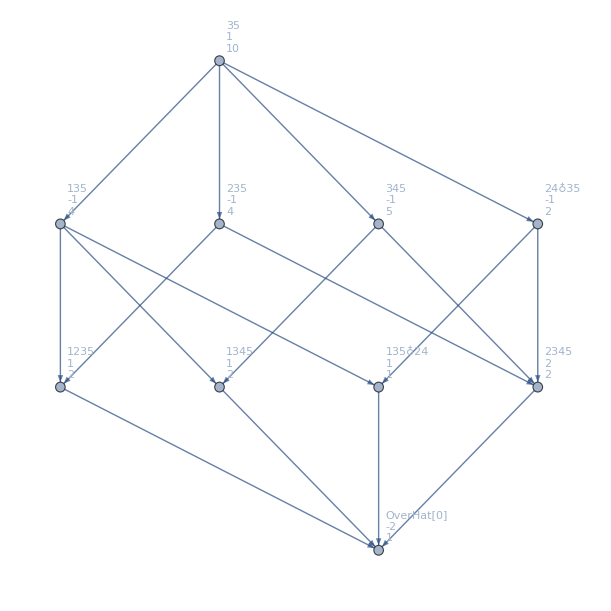

```mathematica
MobiusGraph5[7657,allGraphs5]
```

```mathematica
1*10-(1*4+1*4+1*5+1*2)+(1*2+1*2+1*1+2*2)-(2*1)
```

2

```mathematica
repEmpty=Table[allGraphs5[k,"colofourrealnull"]->allGraphs5[k,"atleast"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→34,n12x3x4x5→13,n123x4x5→5,n1234x5→2,n12345→1,n1235x4→2,n123x45→2,n124x3x5→4,n1245x3→2,n124x35→1,n125x3x4→5,n125x34→2,n12x34x5→5,n12x345→2,n12x35x4→4,n12x3x45→5,n13x2x4x5→10,n134x2x5→4,n1345x2→2,n134x25→1,n135x2x4→4,n135x24→1,n13x24x5→2,n13x245→1,n13x25x4→2,n13x2x45→4,n14x2x3x5→10,n145x2x3→5,n145x23→2,n14x23x5→4,n14x235→1,n14x25x3→2,n14x2x35→2,n15x2x3x4→13,n15x23x4→5,n15x234→2,n15x24x3→4,n15x2x34→5,n1x23x4x5→13,n1x234x5→5,n1x2345→2,n1x235x4→4,n1x23x45→5,n1x24x3x5→10,n1x245x3→4,n1x24x35→2,n1x25x3x4→10,n1x25x34→4,n1x2x34x5→13,n1x2x345→5,n1x2x35x4→10,n1x2x3x45→13}

```mathematica
repFull=Table[allGraphs5[k,"colofour"]->allGraphs5[k,"atleast"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→0,v1x2x3x45→0,v1x2x35x4→0,v1x2x34x5→0,v1x2x345→1,v1x25x3x4→0,v1x25x34→0,v1x24x3x5→0,v1x24x35→0,v1x245x3→0,v1x23x4x5→0,v1x23x45→1,v1x235x4→0,v1x234x5→1,v1x2345→1,v15x2x3x4→0,v15x2x34→1,v15x24x3→0,v15x23x4→1,v15x234→1,v14x2x3x5→0,v14x2x35→0,v14x25x3→0,v14x23x5→0,v14x235→0,v145x2x3→1,v145x23→1,v13x2x4x5→0,v13x2x45→0,v13x25x4→0,v13x24x5→0,v13x245→0,v135x2x4→0,v135x24→0,v134x2x5→0,v134x25→0,v1345x2→1,v12x3x4x5→0,v12x3x45→1,v12x35x4→0,v12x34x5→1,v12x345→1,v125x3x4→1,v125x34→1,v124x3x5→0,v124x35→0,v1245x3→1,v123x4x5→1,v123x45→1,v1235x4→1,v1234x5→1,v12345→1}

```mathematica
allGraphs5[ 7657,"colofourrealnull"]/.repEmpty
```

2

```mathematica
Select[Keys[allGraphs5],(allGraphs5[ #,"colofourrealnull"]/.repEmpty)  <0&]
```

{29520,29523,29524,29521,29514,29515,29512,29496,29497,29442,29443,29433,29434,29280,29281,29278,29271,29272,29269,29254,29200,28791,28794,28795,28792,28785,28786,28767,28768,28552,27336,27337,27327,27328,26608,22963,22954,22720,22711,22234,9840,9841,9832,9814,9760,9598,9589,9571,9517,9111,9112,8869,7654,6925,3280,2551}

```mathematica
Map[{(allGraphs5[ #,"colofourrealnull"]/.repEmpty),(allGraphs5[ #,"colofour"]/.repFull)}->ShowGraph2[#]&, 
Select[Keys[allGraphs5],((allGraphs5[ #,"colofourrealnull"]/.repEmpty)  <0)&&ToString[allGraphs5[ #,"comp"]]=="Greater"&]]
```

{{-1,1}→-Graphics-292801,{-1,1}→-Graphics-292711,{-1,1}→-Graphics-287851,{-1,1}→-Graphics-287861,{-1,1}→-Graphics-285521,{-1,1}→-Graphics-98401,{-1,1}→-Graphics-98321,{-1,1}→-Graphics-95891,{-1,1}→-Graphics-91111,{-1,1}→-Graphics-88691}

```mathematica
allGraphs5[29271,"colofourrealnull"]
```

8 n12345-2 n1234x5-4 n1235x4+n123x4x5-4 n1245x3-2 n124x35+2 n124x3x5+2 n125x3x4+n12x35x4-n12x3x4x5-2 n1345x2-n134x25+n134x2x5-2 n135x24+2 n135x2x4-n13x245+n13x24x5+n13x25x4-n13x2x4x5+n145x2x3-n14x235+n14x25x3+n14x2x35-n14x2x3x5+n15x24x3-n15x2x3x4-n1x2345+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5

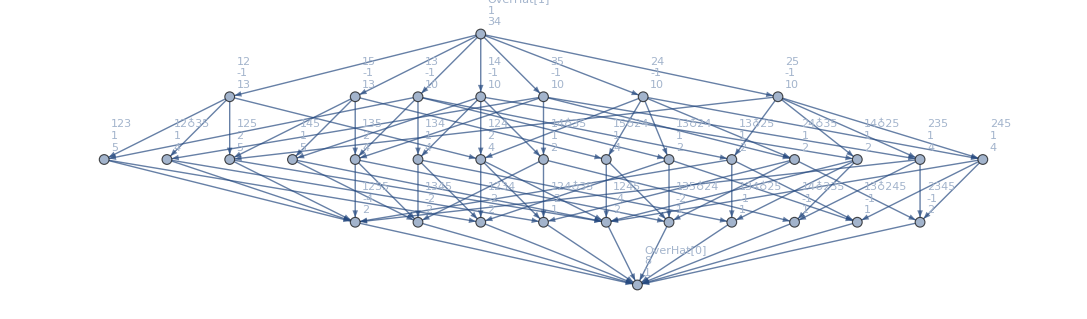

```mathematica
MobiusGraph5[29271,allGraphs5]
```

```mathematica
Map[{(allGraphs5[ #,"colofourrealnull"]/.repEmpty),(allGraphs5[ #,"colofour"]/.repFull)}->ShowGraph2[#]&, Select[Keys[allGraphs5],allGraphs5[#,"atleast"]==0&]]//Sort
```

{{-2,0}→-Graphics-295140,{-2,0}→-Graphics-292720,{-2,0}→-Graphics-287940,{-2,0}→-Graphics-95980,{-2,0}→-Graphics-91120,{-2,0}→-Graphics-295230,{-2,0}→-Graphics-295150,{-2,0}→-Graphics-292810,{-2,0}→-Graphics-287950,{-2,0}→-Graphics-98410,{-2,0}→-Graphics-295240,{-1,0}→-Graphics-294330,{-1,0}→-Graphics-292690,{-1,0}→-Graphics-287910,{-1,0}→-Graphics-287670,{-1,0}→-Graphics-273270,{-1,0}→-Graphics-227110,{-1,0}→-Graphics-95710,{-1,0}→-Graphics-95170,{-1,0}→-Graphics-69250,{-1,0}→-Graphics-25510,{-1,0}→-Graphics-295200,{-1,0}→-Graphics-295120,{-1,0}→-Graphics-294960,{-1,0}→-Graphics-294420,{-1,0}→-Graphics-294340,{-1,0}→-Graphics-292780,{-1,0}→-Graphics-292540,{-1,0}→-Graphics-292000,{-1,0}→-Graphics-287920,{-1,0}→-Graphics-287680,{-1,0}→-Graphics-273360,{-1,0}→-Graphics-273280,{-1,0}→-Graphics-266080,{-1,0}→-Graphics-229540,{-1,0}→-Graphics-227200,{-1,0}→-Graphics-222340,{-1,0}→-Graphics-98140,{-1,0}→-Graphics-97600,{-1,0}→-Graphics-76540,{-1,0}→-Graphics-32800,{-1,0}→-Graphics-295210,{-1,0}→-Graphics-294970,{-1,0}→-Graphics-294430,{-1,0}→-Graphics-273370,{-1,0}→-Graphics-229630,{0,0}→-Graphics-514780,{0,0}→-Graphics-319840,{0,0}→-Graphics-368980,{0,0}→-Graphics-361940,{0,0}→-Graphics-383080,{0,0}→-Graphics-354060,{0,0}→-Graphics-338340,{0,0}→-Graphics-249220,{0,0}→-Graphics-116800,{0,0}→-Graphics-4480,{0,0}→-Graphics-361380,{0,0}→-Graphics-360300,{0,0}→-Graphics-314920,{0,0}→-Graphics-314440,{0,0}→-Graphics-354340,{0,0}→-Graphics-339160,{0,0}→-Graphics-251680,{0,0}→-Graphics-223180,{0,0}→-Graphics-119500,{0,0}→-Graphics-77380,{0,0}→-Graphics-361660,{0,0}→-Graphics-361120,{0,0}→-Graphics-317380,{0,0}→-Graphics-317140,{0,0}→-Graphics-296080,{0,0}→-Graphics-492070,{0,0}→-Graphics-297670,{0,0}→-Graphics-295330,{0,0}→-Graphics-302530,{0,0}→-Graphics-295250,{0,0}→-Graphics-287640,{0,0}→-Graphics-272460,{0,0}→-Graphics-227080,{0,0}→-Graphics-94900,{0,0}→-Graphics-3640,{0,0}→-Graphics-294930,{0,0}→-Graphics-294390,{0,0}→-Graphics-294310,{0,0}→-Graphics-291970,{0,0}→-Graphics-291730,{0,0}→-Graphics-287650,{0,0}→-Graphics-273330,{0,0}→-Graphics-273250,{0,0}→-Graphics-273090,{0,0}→-Graphics-272550,{0,0}→-Graphics-272470,{0,0}→-Graphics-266050,{0,0}→-Graphics-265810,{0,0}→-Graphics-229510,{0,0}→-Graphics-228730,{0,0}→-Graphics-227170,{0,0}→-Graphics-226930,{0,0}→-Graphics-226390,{0,0}→-Graphics-222070,{0,0}→-Graphics-200470,{0,0}→-Graphics-97330,{0,0}→-Graphics-76270,{0,0}→-Graphics-32530,{0,0}→-Graphics-31990,{0,0}→-Graphics-10930,{0,0}→-Graphics-294940,{0,0}→-Graphics-294400,{0,0}→-Graphics-294160,{0,0}→-Graphics-273340,{0,0}→-Graphics-273100,{0,0}→-Graphics-272560,{0,0}→-Graphics-229600,{0,0}→-Graphics-229360,{0,0}→-Graphics-228820,{0,0}→-Graphics-207760,{1,0}→-Graphics-514750,{1,0}→-Graphics-492100,{1,0}→-Graphics-382810,{1,0}→-Graphics-319540,{1,0}→-Graphics-368170,{1,0}→-Graphics-297970,{1,0}→-Graphics-360860,{1,0}→-Graphics-303340,{1,0}→-Graphics-296330,{1,0}→-Graphics-295600,{1,0}→-Graphics-317080,{1,0}→-Graphics-296020,{1,0}→-Graphics-360580,{1,0}→-Graphics-316840,{1,0}→-Graphics-294460,{1,0}→-Graphics-360040,{1,0}→-Graphics-273640,{1,0}→-Graphics-273400,{1,0}→-Graphics-230440,{1,0}→-Graphics-229900,{1,0}→-Graphics-360850,{1,0}→-Graphics-317110,{1,0}→-Graphics-296050,{1,0}→-Graphics-295510,{1,0}→-Graphics-295270,{2,0}→-Graphics-360570,{2,0}→-Graphics-295740,{2,0}→-Graphics-360030,{2,0}→-Graphics-314650,{2,0}→-Graphics-314410,{2,0}→-Graphics-291760,{2,0}→-Graphics-288730,{2,0}→-Graphics-273550,{2,0}→-Graphics-353260,{2,0}→-Graphics-272820,{2,0}→-Graphics-251380,{2,0}→-Graphics-229810,{2,0}→-Graphics-338080,{2,0}→-Graphics-227440,{2,0}→-Graphics-223150,{2,0}→-Graphics-200500,{2,0}→-Graphics-119200,{2,0}→-Graphics-97630,{2,0}→-Graphics-76570,{2,0}→-Graphics-11740,{2,0}→-Graphics-360840,{2,0}→-Graphics-295420,{2,0}→-Graphics-295770,{2,0}→-Graphics-294690,{2,0}→-Graphics-314680,{2,0}→-Graphics-293050,{2,0}→-Graphics-292570,{2,0}→-Graphics-353530,{2,0}→-Graphics-288760,{2,0}→-Graphics-338890,{2,0}→-Graphics-251410,{2,0}→-Graphics-222370,{2,0}→-Graphics-119470,{2,0}→-Graphics-77350,{2,0}→-Graphics-98440,{3,0}→-Graphics-353250,{3,0}→-Graphics-288450,{3,0}→-Graphics-272730,{3,0}→-Graphics-338070,{3,0}→-Graphics-248950,{3,0}→-Graphics-227350,{3,0}→-Graphics-116770,{3,0}→-Graphics-94930,{3,0}→-Graphics-4450,{3,0}→-Graphics-3670,{3,0}→-Graphics-294600,{3,0}→-Graphics-292960,{3,0}→-Graphics-292230,{3,0}→-Graphics-353520,{3,0}→-Graphics-288480,{3,0}→-Graphics-338880,{3,0}→-Graphics-248980,{3,0}→-Graphics-219670,{3,0}→-Graphics-331570,{3,0}→-Graphics-77070,{3,0}→-Graphics-117040,{3,0}→-Graphics-95740,{3,0}→-Graphics-70060,{3,0}→-Graphics-53770,{3,0}→-Graphics-25540}